{-4.78964×10^-13-1.5748×10^-14 ⅈ}

{5.21775×10^-16}

{2.71491×10^-8}

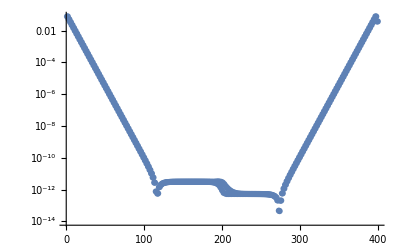

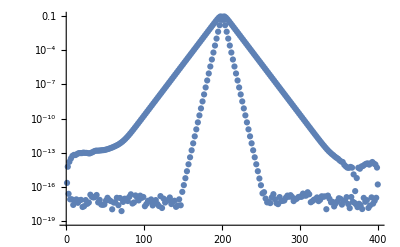

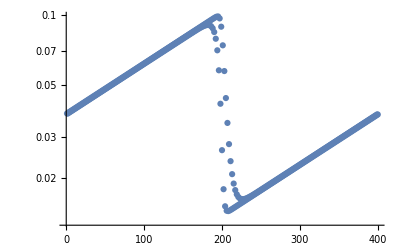

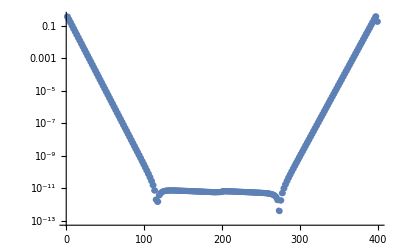

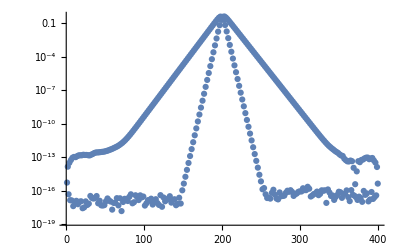

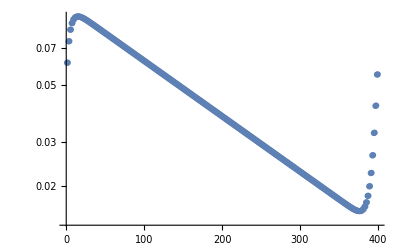

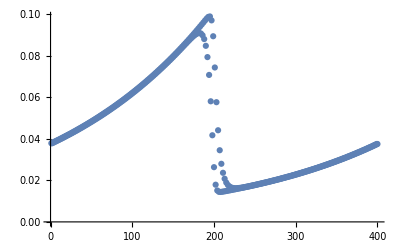

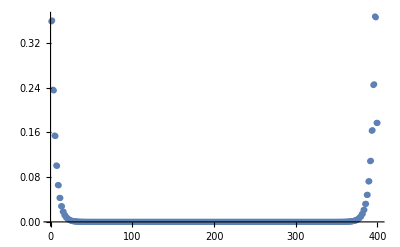

```mathematica
Ntval=200;h1val = 4.0; h2val = 4.0;h3val=4.0;h4val=4.0;Elval=0.0;Eaval=1.0;
s1val = 100.0;s2val =1.0;t1val = 1;t2val = 2.5; b1val = 2.5;b2val = 1.0;λval=0.01;
W0=WRectangleAllLinksW0SSH[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
W0i=Inverse[W0];
W1=WRectangleAllLinksW1SSH[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
WB=WRectangleAllLinksWB[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
WF1=W1+W0i.WB;
Eigenvalues[W0.WF1,-1]
Abs[Eigenvalues[W0.WF1,-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}]]
Abs[Eigenvalues[HRectangle[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}]]

u1=Eigenvectors[WF1.W0][[2*Ntval]];
v1=Eigenvectors[Transpose[WF1.W0]][[2*Ntval]];
u0=Eigenvectors[W0.WF1][[2*Ntval]];
v0=Eigenvectors[Transpose[W0.WF1]][[2*Ntval]];
ListLogPlot[Abs[u1 v1]/Abs[u1.v1],PlotRange->All]
ListLogPlot[Abs[u0 v0 ]/Abs[u0.v0],PlotRange->All]
ListLogPlot[Abs[u1],PlotRange->All]
ListLogPlot[Abs[v1],PlotRange->All]
ListLogPlot[Abs[u0],PlotRange->All]
ListLogPlot[Abs[v0],PlotRange->All]
ListPlot[Re[u1],PlotRange->All]
ListPlot[Re[v1],PlotRange->All]
ListPlot[Re[u0],PlotRange->All]
ListPlot[Re[v0],PlotRange->All]
```

```mathematica
λ1=λup[2,1,2,1,s1val/(1+Exp[-EtIn1[20,Ntval,1,s2val,1.0]]),s1val/(1+Exp[EtIn1[20,Ntval,1,s2val,1.0]])]
```

0.6835

{0.051984-1.10888×10^-9 ⅈ}

{2.22056×10^-14}

{2.22063×10^-14}

1.28868

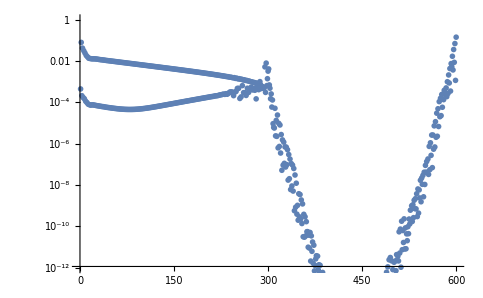

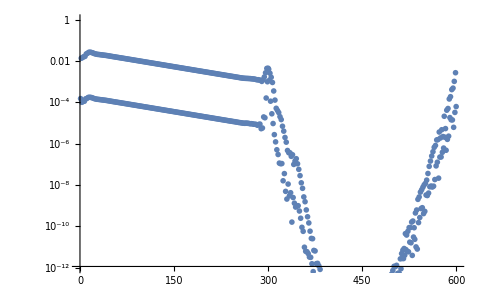

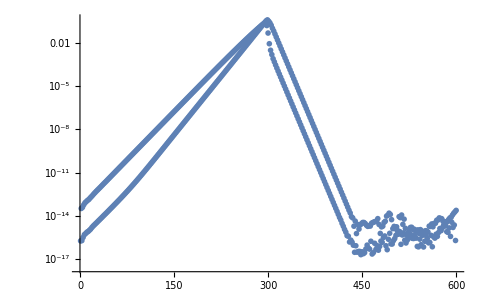

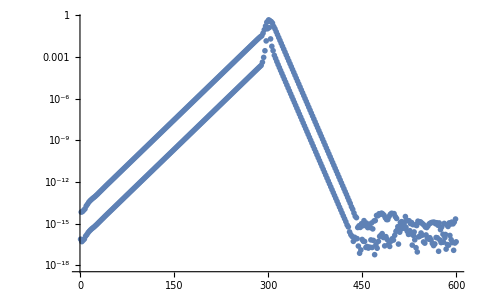

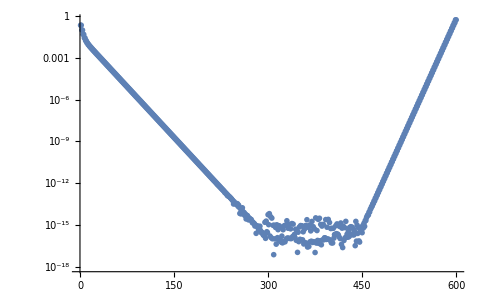

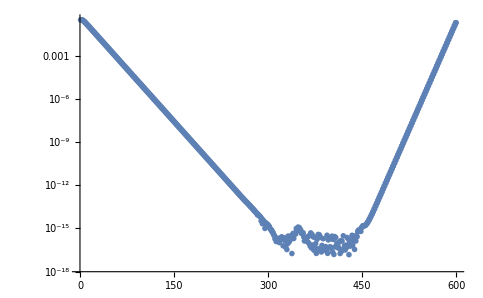

```mathematica
Ntval=200;h1val = 1.0; h2val = 1.0;h3val=1.0;h4val=1.0;Elval=0.0;Eaval=1.0;
s1val = 100.0;s2val =1.0;t1val = 1;t2val = 2.0; b1val = 2.0;b2val = 1.0;λval=0.25;
W0=WRectangleAllLinksW0SSH[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
W0i=Inverse[W0];
W1=WRectangleAllLinksW1SSH[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
WB=WRectangleAllLinksWB[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval/2];
WF1=W1+W0i.WB;
Eigenvalues[W0.WF1,-1]
Abs[Eigenvalues[W0.WF1,-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}]]
Abs[Eigenvalues[HRectangle[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval],-1,Method->{"Arnoldi",BasisSize->120,MaxIterations->100000,Tolerance->Automatic}]]

u1=Eigenvectors[WF1.W0][[2*Ntval]];
v1=Eigenvectors[Transpose[WF1.W0]][[2*Ntval]];
u0=Eigenvectors[W0.WF1][[2*Ntval]];
v0=Eigenvectors[Transpose[W0.WF1]][[2*Ntval]];
Total[Abs[u1 v1]/Abs[u1.v1]]
ListLogPlot[Abs[u1 v1]/Abs[u1.v1],PlotRange->{{0,2 Ntval},{10^(-12),1}}]
ListLogPlot[Abs[u0 v0 ]/Abs[u0.v0],PlotRange->{{0,2 Ntval},{10^(-12),1}}]
ListLogPlot[Abs[u1],PlotRange->All]
ListLogPlot[Abs[u0],PlotRange->All]
ListLogPlot[Abs[v1],PlotRange->All]
ListLogPlot[Abs[v0],PlotRange->All]
```

```mathematica
Total[Abs[u1 v1]]
```

0.150145

```mathematica
Abs[u1.v1]
```

0.150145

```mathematica
Abs[u1 v1]/Abs[u1.v1]
```

{0.0763274,0.0887006,0.0392832,0.0447933,0.0198586,0.0226274,0.0100333,0.0114316,0.00507022,0.00577669,0.00256333,0.0029204,0.00129708,0.00147769,0.000657494,0.000748985,0.000334434,0.000380916,0.000171255,0.000195005,0.0000888323,0.000101098,0.0000472005,0.0000536589,0.0000261727,0.0000296841,0.0000155561,0.0000175475,0.0000102317,0.000011421,6.54965×10^-6,7.11111×10^-6,5.09687×10^-6,5.15238×10^-6,5.57397×10^-6,4.70625×10^-6,4.67343×10^-6,2.5729×10^-6,4.60632×10^-6,7.99441×10^-7,6.85928×10^-6,5.10774×10^-7,9.16484×10^-6,8.6442×10^-7,0.0000117993,1.92009×10^-6,0.0000132133,3.54578×10^-6,0.0000172379,7.12584×10^-6,0.000020582,0.0000125259,0.0000310828,0.0000248011,0.0000518152,0.0000491208,0.0000928333,0.00009727,0.000174027,0.000192596,0.000334771,0.000381321,0.00065301,0.000754956,0.00128307,0.00149467,0.00253047,0.00295915,0.0050001,0.00585848,0.00988953,0.0115985,0.0195697,0.0229619,0.0387352,0.0454275,0.0766991,0.0882709,0.152877,0.176804}

```mathematica
WperiodicRot2[a_,ϵ1_,ϵ2_,λ_,k_]:={{(Exp[λ/2]- Exp[-λ/2]*Exp[I k])ϵ1-1/factor[k,λ],a/factor[k,λ]},{-(Exp[λ/2]- Exp[-λ/2]*Exp[I k]),(Exp[λ/2]- Exp[-λ/2]*Exp[I k])-1/(ϵ2*factor[k,λ])}}
WperiodicRot3[a_,ϵ1_,ϵ2_,λ_,k_]:={{(Exp[λ/2]- Exp[-λ/2]*Exp[I k])ϵ1-1/factor[k,λ],a/factor[k,λ]},{-(Exp[λ/2]- Exp[-λ/2]*Exp[I k]),(Exp[λ/2]- Exp[-λ/2]*Exp[I k])-1/(ϵ2*factor[k,λ])}}*factor[k,λ]
```

```mathematica
MatrixForm[WperiodicRot2[a,ϵ1,ϵ2,λ,k]]
FullSimplify[MatrixForm[WperiodicRot3[a,ϵ1,ϵ2,λ,k]]]
```

(-1/(ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2))+(-ⅇ^(ⅈ k-λ/2)+ⅇ^(λ/2)) ϵ1 | a/(ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2))
ⅇ^(ⅈ k-λ/2)-ⅇ^(λ/2) | -ⅇ^(ⅈ k-λ/2)+ⅇ^(λ/2)-1/((ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2)) ϵ2))

(-1-2 ϵ1+2 ϵ1 Cos[k+ⅈ λ] | a
2-2 Cos[k+ⅈ λ] | -2-1/ϵ2+2 Cos[k+ⅈ λ])

```mathematica
WindingRot1[a_,ϵ1_,ϵ2_,λ_]:=Table[{Re[Det[Conjugate[WperiodicRot2[a,ϵ1,ϵ2,λ,i]]]],Im[Det[Conjugate[WperiodicRot2[a,ϵ1,ϵ2,λ,i]]]]},{i,-π,π,0.001}]
WindingRot2[a_,ϵ1_,ϵ2_,λ_]:=Table[{i/(2*π),Im[Log[Det[Conjugate[WperiodicRot2[a,ϵ1,ϵ2,λ,i]]]]]},{i,-π,π,0.01}]
WindingRot3[a_,ϵ1_,ϵ2_,λ_]:=Table[{i,Re[Det[Conjugate[WperiodicRot2[a,ϵ1,ϵ2,λ,i]]]]},{i,0,π,0.001}]
WindingRot4[a_,ϵ1_,ϵ2_,λ_]:=Table[{i,Im[Det[Conjugate[WperiodicRot2[a,ϵ1,ϵ2,λ,i]]]]},{i,-π,π,0.001}]
```

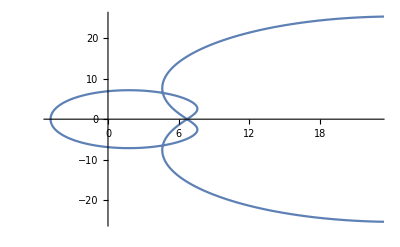

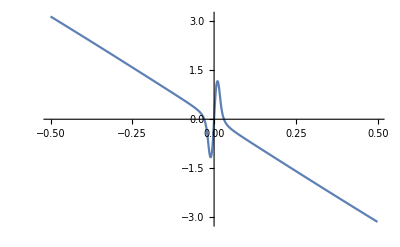

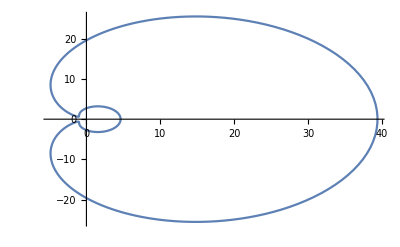

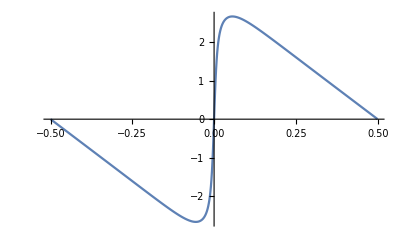

```mathematica
ListPlot[WindingRot1[10,1,10,-0.05],Joined->True]
ListPlot[WindingRot2[10,1,10,-0.05],PlotRange->All,Joined->True]
ListPlot[WindingRot1[0.5,1,10,-0.05],Joined->True,PlotRange->All]
ListPlot[WindingRot2[0.5,1,10,-0.05],PlotRange->All,Joined->True]
```

```mathematica
Ntval=1800;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Elval=0.0;Eaval=1/10;
s1val =1/10;s2val =1.0;t1val = 1;t2val = 1.0; b1val = 1.0;b2val = 1;λval=-0.1;ϵval=0.05
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval];
ListLogPlot[Abs[Eigenvalues[WF1,-40,Method->"Arnoldi"]],PlotRange->All]
ListPlot[Abs[Eigenvalues[WF1]],PlotRange->All]
```

0.05

$Aborted

$Aborted

```mathematica
Ntval=10000;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Elval=0.0;Eaval=1/10;
s1val =0.5;s2val =1.0;t1val = 1;t2val = 1.0; b1val = 1.0;b2val = 1;λval=-0.0;ϵval=0.05
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval];
ListLogPlot[Abs[Eigenvalues[WF1,-40,Method->"Arnoldi"]],PlotRange->All]
```

0.05

```mathematica
Abs[Eigenvalues[WF1]]
```

{6.03294,6.02951,6.0238,6.01581,6.00556,5.99304,5.97827,5.96127,5.94205,5.92062,5.89701,5.87124,5.84333,5.8133,5.78118,5.74701,5.71081,5.67262,5.63246,5.59038,5.54641,5.5006,5.45299,5.40361,5.35251,5.29974,5.24535,5.18939,5.1319,5.07294,5.01257,4.95084,4.8878,4.82351,4.75803,4.69143,4.62376,4.55509,4.48548,4.41499,4.3437,4.27166,4.19896,4.12565,4.0518,3.9775,3.90281,3.8278,3.75255,3.67714,3.60164,3.52615,3.45074,3.37551,3.30057,3.2261,3.15238,3.08052,3.06507,3.06271,3.05841,3.05316,3.04537,3.0376,3.02613,3.01816,3.00484,3.0012,2.98321,2.97081,2.95009,2.94132,2.92203,2.91163,2.88553,2.87308,2.84914,2.8401,2.80893,2.79709,2.76972,2.75774,2.72212,2.71576,2.68248,2.66748,2.63142,2.62646,2.58573,2.57514,2.53961,2.52561,2.48567,2.48003,2.43606,2.42708,2.38765,2.37344,2.33412,2.32367,2.27825,2.27361,2.22799,2.21716,2.17712,2.16183,2.12319,2.10939,2.06646,2.05869,2.01005,2.00705,1.95931,1.94994,1.90878,1.89336,1.85751,1.83847,1.8053,1.78536,1.75235,1.73372,1.6992,1.68311,1.64642,1.63325,1.59448,1.58394,1.54374,1.5351,1.49448,1.48664,1.44693,1.43852,1.40122,1.3908,1.35739,1.34363,1.31547,1.29727,1.2753,1.25256,1.2362,1.21191,1.19585,1.177,1.15255,1.14643,1.11797,1.10953,1.09281,1.07384,1.06209,1.0536,1.0369,1.02471,1.01829,1.01351,1.00589,1.00151,0.975773,0.933067,0.890969,0.8496,0.809031,0.769317,0.730508,0.69265,0.655784,0.619952,0.585189,0.55153,0.519006,0.487648,0.457482,0.428531,0.400815,0.374354,0.34916,0.325245,0.302616,0.281278,0.261229,0.242465,0.22498,0.20876,0.193791,0.180051,0.167518,0.156165,0.145961,0.136876,0.128873,0.12192,0.115981,0.111023,0.107014,0.103927,0.101739,0.100434}

0.05

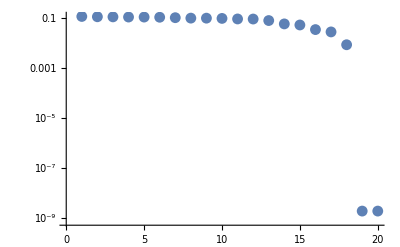

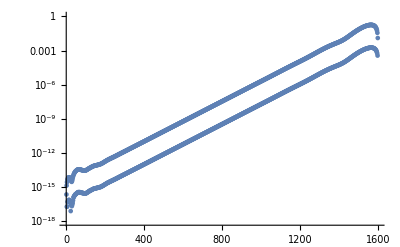

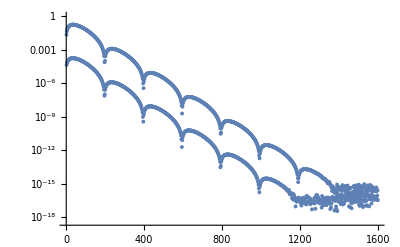

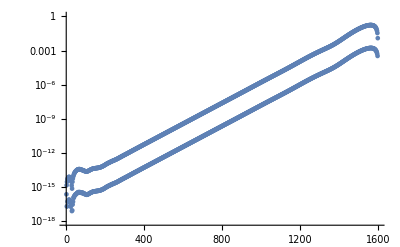

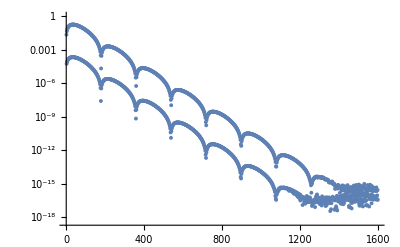

```mathematica
Ntval=800;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Elval=0.0;Eaval=1.0/10;
s1val = 100;s2val =1.0;t1val = 1;t2val = 1.0; b1val = 1.0;b2val = 1;λval=0.05;ϵval=0.05
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val,t2val, b1val, b2val, h1val, h2val,h3val,h4val,Eaval,Elval,Ntval,   ⅈ λval];
ListLogPlot[Abs[Eigenvalues[WF1,-20,Method->"Arnoldi"]],PlotRange->All]
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]]]
ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]]]
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval-1]]]]
ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval-1]]]]
```